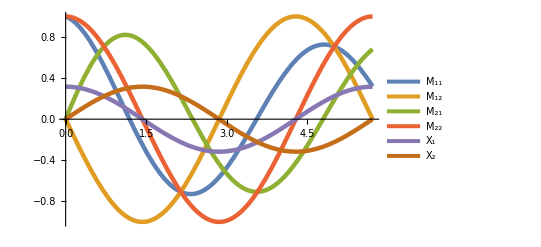

```mathematica
F1[X1_, X2_] = X1/10 - X2^3 - X1*X2^2 - X1^2*X2 - X2 - X1^3;
F2[X1_, X2_] = X1 + X2/10 + X1*X2^2 + X1^3 - X2^3 - X1^2*X2;

J[X1_, X2_] = {{D[F1[X1,X2], X1], D[F1[X1,X2], X2]},{D[F2[X1,X2],X1], D[F2[X1,X2],X2]}};

mu0 = 1/10;
w0 = 1;
v0 = 1;
x0 = Sqrt[mu0];
tMax = 2*Pi/(w0+mu0*v0);

eqns = {{{M11'[t], M12'[t]}, {M21'[t], M22'[t]}} == J[X1[t], X2[t]].{{M11[t],M12[t]},{ M21[t], M22[t]}},
X1'[t] == F1[X1[t], X2[t]],
X2'[t] == F2[X1[t], X2[t]],
M11[0] == 1,
M12[0] == 0,
M21[0]== 0,
M22[0] == 1,
X2[0] == 0,
X1[0] == x0};

sol = NDSolve[eqns,{X1[t], X2[t],M11[t],M12[t],M21[t],M22[t]},{t, 0, tMax}];

MT = {{M11[t], M12[t]}, {M21[t], M22[t]}}/.sol[[1]]/.t->tMax;


Show[
Plot[{M11[t]/.sol,M12[t]/.sol, M21[t]/.sol, M22[t]/.sol,X1[t]/.sol,X2[t]/.sol}, 
{t,0,tMax},
PlotStyle->{Thickness[0.008]},
PlotLegends->LineLegend[{"M_11","M_12","M_21","M_22","X_1","X_2"}],
AxesStyle->AbsoluteThickness[2]]
]
```

```mathematica
□/□
```

```mathematica
Log[Eigenvalues[MT]]/tMax
```

{5.78753×10^-9,-0.2}